```mathematica
genSound[ music_]:=(
soundNoteList[list_]:= Apply[SoundNote, list];
generated = Map[soundNoteList, music];
sound = Sound[generated];
Return[sound];
)
```

```mathematica
ApplyAndJoin[fn_, count_]:=(
Flatten[Map[fn, Range[count]]]
)
```

```mathematica
ChooseTone[previous_,weights_,toneWeights_, toneImportance_]:=(
allTones=Range[-Length[weights],Length[weights]]+previous;
allIntervalWeights=Join[Reverse[Drop[weights,-1]],weights];
allToneWeights=Map[Function[t,Part[toneWeights,t % Length[toneWeights]]],allTones];
tone = RandomSample[(allToneWeights * allIntervalWeights) ^ toneImportance -> allTones);
)
```

```mathematica
GetMelody[rythm_, weights_, toneWeights_] := (
melody = {0};
For[i=1, i<Length[rythm],i++, (
previous = Part[melody, i];
interval = RandomSample[weights->{0, 1, 2,3, 4, 5, 6, 7, 8}, 1];
interval = If[RandomReal[]>0.5, interval, -interval];
next = interval+ previous;
AppendTo[melody, next];
)];
Return[melody];
)
```

```mathematica
CreateMusic[melody_, tones_, rythm_] := (
music = {};
For[i=0, i<Length[melody],i++, (
toneOffset = Part[melody, i+1];
tone = Part[tones, 1 + Mod[toneOffset, Length[tones]]] + (Floor[toneOffset / Length[tones]] * 12);
sound = {tone, Part[rythm, i + 1] * 1.5, "Piano"};
AppendTo[music,sound];
)];
Return[music];
)
```

```mathematica
GetTact[divCoef_, recursionCoef_] := (
If[RandomReal[] > divCoef,(
Return[{1}]
),(
divLen[e_] := e / 2;
Return[ Map[divLen, Join[GetTact[divCoef / recursionCoef, recursionCoef], GetTact[divCoef/recursionCoef, recursionCoef]]]];
)]
)
```

```mathematica
GetRythm[divCoef_, recursionCoef_, size_] := 
ApplyAndJoin[Function[i, GetTact[divCoef, recursionCoef]], size]
```

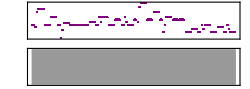

```mathematica
rtm1 = GetRythm[2.3, 3,  1];
rtm2 = GetRythm[2.3, 3,  1];
tones = {0, 2, 3, 5, 7, 8, 10} + 0;
weights = {1, 3, 5, 4, 4, 0.7,0.7, 1.2, 1};
toneWeights={1.7, 1.5, 1.6, 1, 1.6, 1.5, 1};
CmpM[rtm_]:=GetMelody[rtm, weights, toneWeights];
mainM = CmpM[rtm2];
melody1 = Join[CmpM[rtm1], ReplacePart[mainM, Length[rtm2]-> 4], CmpM[rtm1], ReplacePart[mainM, Length[rtm2]->0]];
mainM = CmpM[rtm1];
melody2 = Join[CmpM[rtm2], ReplacePart[mainM, Length[rtm1]-> 4], CmpM[rtm2], ReplacePart[mainM, Length[rtm1]->0]];

genSound[CreateMusic[Join[melody1, melody2, melody1+3, melody2-4],tones,ApplyAndJoin[Function[i, Join[rtm1, rtm2, rtm1, rtm2, rtm2, rtm1, rtm2, rtm1]], 2]]]
```